# Uniswap V3 Pricing Review for Lenders

```mathematica
SeedRandom["0xf2ecf6f0aaf635b6df6404485e749dcad5be4dd1e5bf7b9aac3f06f1245da0f1"]
```

RandomGeneratorState[…]

## Motivation

With the creation of Uniswap, thorough stochastic pricing analysis has been reviewed by Bardoscia and Milionis describing it’s spot pricing dynamics. Since it’s release, only a few protocols have been created to address leveraged perpetual options using Uniswap V3 pricing dynamics, effectively creating a “loan” based on backed collateral for position holders. Below is a review of simulation using Mathematica to generate empirical risk profiles for V3 positions with standard techniques in Stochastic Calculus. If users are to appropriately price loans for Uniswap V3 positions, simulating worst case lower bounds on losses is important and should be taken into consideration with other methods such as backtesting.

## Stochastic Calculus Review

## Ito’s Lemma

Ito' s Lemma allows us to model functions whose variables are random values . For a function F(X,t) where X is a random variable and t is time, Ito’s lemma gives us a way to model a probability density function for the future time t. We call the variables a “process”, and the result of using Ito’s Lemma a new process. The rest of the system utilizes Ito’s Lemma under the hood to derive functions of random variables. It’s not essential to understand these Lemmas, but they are important in stochastic modeling.

### Single Variable Ito’s Lemma

Below is the main statement for Ito’s Lemma.

-Graphics-

### Multivariable Ito’s Lemma

When modeling over multiple variables including time, we need the Multivariable Ito’s Lemma.

-Graphics-

## Uniswap V3 Stochastic Analysis

Now that we have Ito’s Lemma defined, we can use the program to determine some average case and variances for Uniswap’s value functions.

## Uniswap State Equations

Below, are some necessary equations for Uniswap V3 analysis. In these equations, treat Y as a cash-like stable numeraire. Prices are in terms of the numeraire per X token (USD per ETH). p_a represents the lower bound of the position, and p_b is the upper bound.

```mathematica
liquidityEquation = (x + L/(√Subscript[p, b]))(y + L √Subscript[p, a]) == L^2;
tokensGivenLiquidity = { x -> L (√Subscript[p, b]-√p)/(√p * √Subscript[p, b]), y -> L (√p - √Subscript[p, a])};
liquidityGivenTokens = { Subscript[L, x] ->x *(√p * √Subscript[p, b])/(√Subscript[p, b] -√p) , Subscript[L, y] -> y/(√p - √Subscript[p, a])};
```

```mathematica
Liquidity[lowerPriceBound_, upperPriceBound_, currentPrice_, total_] :=
 Solve[
(Subscript[L, x] == Subscript[L, y] /. liquidityGivenTokens /.{x -> holdX , y -> holdY , p -> currentPrice , Subscript[p, a] -> lowerPriceBound, Subscript[p, b] -> upperPriceBound}) &&
holdX >0 && holdY > 0 && total == holdX*currentPrice + holdY, {holdX, holdY}] // ({ x -> holdX, y -> holdY, L -> holdY/(√currentPrice- √lowerPriceBound) } /. #)&;
```

```mathematica
Liquidity[1600, 1700, 1628, 10000] // N
1628*x + y  /. %
```

{{x→4.37661,y→2874.87,L→8249.71}}

{10000.}

```mathematica
originalValue = x*p + y /. tokensGivenLiquidity /. {Subscript[p, a] -> lower, Subscript[p, b] -> higher, p -> startPrice };
currentValue = x*p + y /. tokensGivenLiquidity /.  {Subscript[p, a] -> lower, Subscript[p, b] -> higher};
IL =(currentValue - originalValue)/originalValue;
humanReadable = { lower -> Subscript[p, a], higher -> Subscript[p, b] , startPrice -> Subscript[p, 0]};
IL /. humanReadable // Simplify;
```

## Pricing Derivations for Impermanent Loss

Taking a look at a particular example, we can derive some interesting results with the Uniswap math. Below is a close enough situation to reality using the curves. The block directly below is just a setup

```mathematica
ethDailyVol = 0.0034;
ethMeanYearly = 0.1;
dailyETHmean = ethMeanYearly/365;
currentPrice = 1628;
lowerBound = 1600;
upperBound = 1700;
initialValue = 10000;
currentLiquidityParams =Liquidity[lowerBound, upperBound, currentPrice, initialValue] // N
```

{{x→4.37661,y→2874.87,L→8249.71}}

### Plotting to Understand Value Curves

Let’s load the example into the curves and take a look at them to determine value action across price.

```mathematica
valueCurve =currentValue  /. currentLiquidityParams;
```

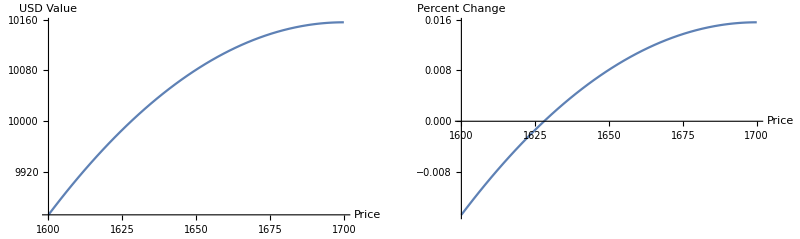

```mathematica
GraphicsGrid[{{
Plot[valueCurve /. { lower -> lowerBound, higher -> upperBound , startPrice -> currentPrice}, {p, lowerBound, upperBound}, AxesLabel->{"Price", "USD Value"}],
Plot[IL /. { lower -> lowerBound, higher -> upperBound , startPrice -> currentPrice}, {p, lowerBound, upperBound},  AxesLabel->{"Price", "Percent Change"}]
}}]
```

#### Closed Form Analysis

Because Wolfram acts symbolically, we can derive some processes directly and compute means and variances.

```mathematica
procPVOpen = TransformedProcess[currentValue /. {p -> p[t]},p \[Distributed] GeometricBrownianMotionProcess[μ, σ, S],
t];
```

```mathematica
meanProcPVOpen = Mean[procPVOpen[t]];
varianceProcPVOpen = Variance[procPVOpen[t]];
```

```mathematica
TableForm[{
{"Mean Function", meanProcPVOpen /. {higher -> Subscript[p, b], lower -> Subscript[p, a]}},
{"Variance", varianceProcPVOpen/. {higher -> Subscript[p, b], lower -> Subscript[p, a]}}
}]
```

Mean Function | L (2 ⅇ^(1/8 t (4 μ-σ^2)) √S-√p_a-(ⅇ^(t μ) S)/(√p_b))
Variance | (ⅇ^(t (μ-σ^2/4)) (-1+ⅇ^((t σ^2)/4)) L^2 S ((ⅇ^(t (μ+(3 σ^2)/4))+ⅇ^(t (μ+σ^2))+ⅇ^(1/4 t (4 μ+σ^2))+ⅇ^(t μ+(t σ^2)/2)) S-4 ⅇ^(1/8 t (4 μ+σ^2)) (1+ⅇ^((t σ^2)/4)) √S √p_b+4 p_b))/p_b

Above supplies a closed form mean and variance of the values.

```mathematica
realizedDistribution = procPVOpen /. {μ -> ethMeanYearly/365, σ -> ethDailyVol, S -> currentPrice, higher -> upperBound, lower -> lowerBound} /. currentLiquidityParams[[1]];
realizedSamples = SliceDistribution[realizedDistribution,90] //
RandomVariate[#,1000]& //
Map[(# -10000)/10000&] ;
```

```mathematica
realizedSamples // {Mean[#], Median[#], Quantile[#,{1/20,1/4,3/4, 19/20}]}&
```

{0.00344573,0.00957961,{-0.0296404,-0.000634804,0.0141588,0.0155399}}

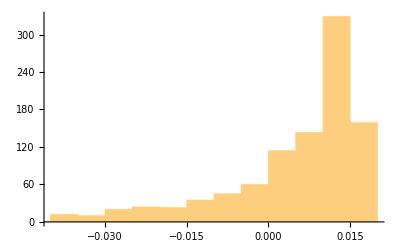

```mathematica
Histogram[realizedSamples]
```

From this we have a clear closed form solution for the mean and variance, so one can produce 95% confidence intervals.

## Further Discussions

Much of this was inspired by the papers below. Since this is more about sampling and not mathematical proofs, readers should take a look at the analysis below for better metrics.

```mathematica
TableForm[{
{"Impermanent Loss in Uniswap V3", Hyperlink["https://lambert-guillaume.medium.com/an-analysis-of-the-expected-value-of-the-impermanent-loss-in-uniswap-bfbfebbefed2"]},
{"Uniswap Liquidity V3 Math", Hyperlink["http://atiselsts.github.io/pdfs/uniswap-v3-liquidity-math.pdf"]}
}]
```

Impermanent Loss in Uniswap V3 | https://lambert-guillaume.medium.com/an-analysis-of-the-expected-value-of-the-impermanent-loss-in-uniswap-bfbfebbefed2
Uniswap Liquidity V3 Math | http://atiselsts.github.io/pdfs/uniswap-v3-liquidity-math.pdf

## Perpetual Lending Stochastic Analysis

## Mean-Reverting Additional Value Term

Below we use the same techniques to add an additional interest rate using the Ornstien Uhlenbeck proccess. This model is similar to a perpetual option where it does fluxuate, but is mean reverting assuming a standard 2% per year interest rate.

```mathematica
100 (1 -ⅇ^-0.02)
```

1.98013

```mathematica
borrowedCapital = 10000;
borrowDailyRate = 0.02/365;
borrowRateDailyVol = borrowDailyRate/20;
orResponseTerm = 0.2;
mrModel = currentValue - borrowedCapital (1 -ⅇ^(-r[t]*t))/. {p -> p[t], higher -> upperBound, lower -> lowerBound} /. currentLiquidityParams[[1]] // Simplify
```

-339988.+10000. ⅇ^(-t r[t])+16499.4 √p[t]-200.085 p[t]

We can see we have a viable closed form model. Below is a histogram of values.

```mathematica
realizedProcMR = TransformedProcess[ mrModel ,{
p \[Distributed] GeometricBrownianMotionProcess[ethMeanYearly/365, ethDailyVol, currentPrice],
r \[Distributed] OrnsteinUhlenbeckProcess[borrowDailyRate,borrowRateDailyVol, orResponseTerm, borrowDailyRate]
},t]
```

TransformedProcess[-339988.+10000. ⅇ^(-t p2[t])+16499.4 √p1[t]-200.085 p1[t],{p1\[Distributed]GeometricBrownianMotionProcess[0.000273973,0.0034,1628],p2\[Distributed]OrnsteinUhlenbeckProcess[0.0000547945,2.73973×10^-6,0.2,0.0000547945]},t]

{-0.00082362,0.00523417,{-0.0308813,-0.00557974,0.0094681,0.010742}}

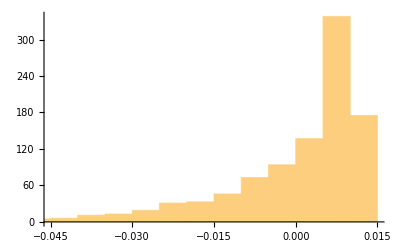

```mathematica
samplesMRDistribution = SliceDistribution[realizedProcMR, 90] //
RandomVariate[#, 1000]&  // Map[(# - 10000)/10000&];
stats = samplesMRDistribution// {Mean[#], Median[#], Quantile[#,{1/20,1/4,3/4, 19/20}]}&

Histogram[samplesMRDistribution]
```